## wczytanie danych

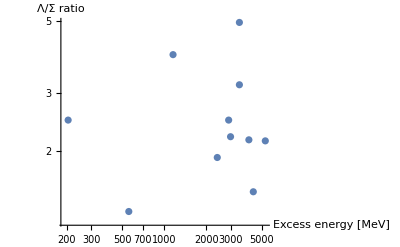

FittedModel[224.294 (-2.55+x)+81.999 (-2.55+x)^2]

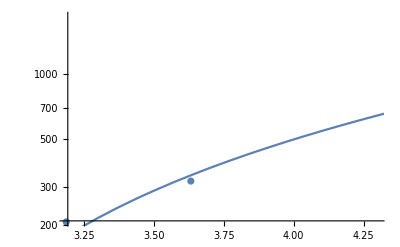

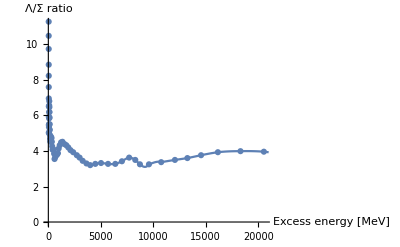

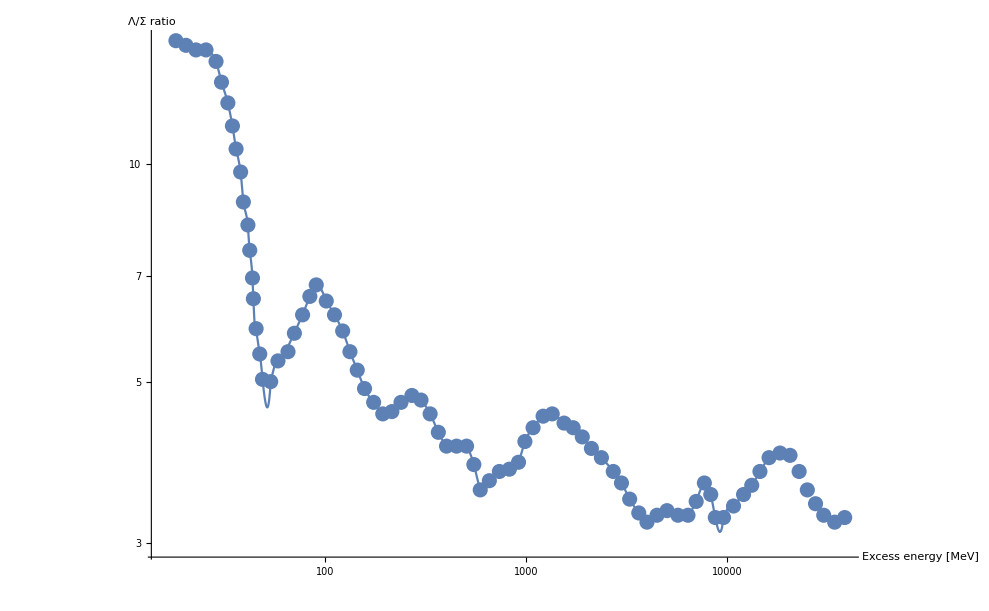

```mathematica
SetDirectory["/home/krzysztof/Dropbox/Doktorat/Przekroje/Obrazki"];
lista=Import["LambdaDig.dat"];
lambda1115=Delete[lista,2];
lambdatosigma=Import["LamToSig.dat"];
ListLogLogPlot[lambdatosigma,AxesLabel->{"Excess energy [MeV]","Λ/Σ ratio"}]

urqmd=Import["UrQmDdig.dat","Data"];
lambda1115fit=NonlinearModelFit[lambda1115,a*(x-2.55)+b*(x-2.55)^2,{a,b},x]
Show[
ListLogPlot[lambda1115,PlotRange->{{2.9,6.2},{0,21000}}],
LogPlot[lambda1115fit[x],{x,2.9,6.2}]
]
urqmdFit=Interpolation[urqmd,InterpolationOrder->3];
Show[
ListPlot[urqmd,AxesLabel->{"Excess energy [MeV]","Λ/Σ ratio"}],
Plot[urqmdFit[x],{x,20,21000}]
]
Show[
ListLogLogPlot[urqmd,AxesLabel->{"Excess energy [MeV]","Λ/Σ ratio"},LabelStyle->Large],
LogLogPlot[urqmdFit[x],{x,20,21000}]
]
```

## Ξ production

InterpolatingFunction::dmval: Input value {0.0408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0000408163} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

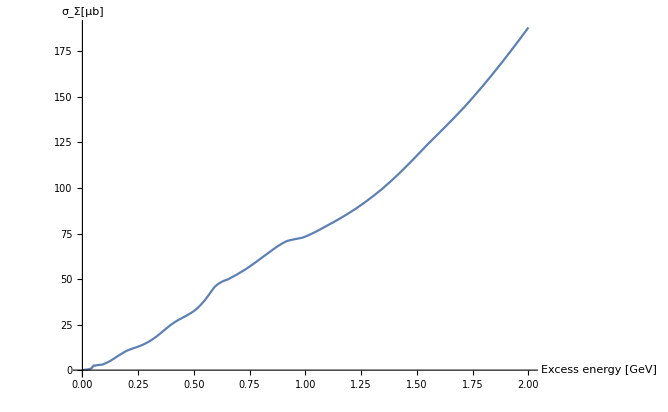

```mathematica
sigma0[e_]:=lambda1115fit[e+2.55]/urqmdFit[e*1000]; (*przekrój na sigmę w funkcji energii nad progiem, uwaga na jednostki!*)
Plot[sigma0[e],{e,0,2},AxesLabel->{"Excess energy [GeV]","σ_Σ[μb]"},LabelStyle->Large]
```

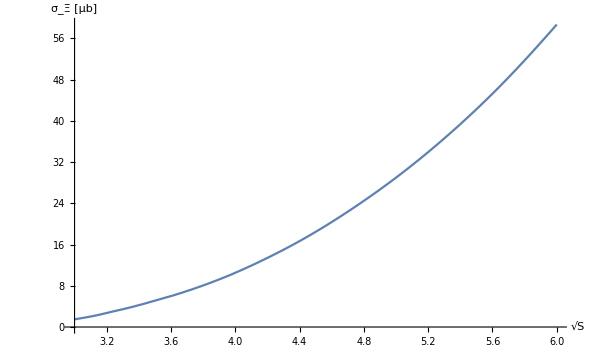

4.7534

```mathematica
ksiCS[s_]:=0.44*(1-(2.2/s)^0.027)^0.780*(lambda1115fit[s]+sigma0[s-2.62]);
Plot[ksiCS[x],{x,3,6},AxesLabel->{Sqrt[S],"σ_Ξ [μb]"},LabelStyle->Large]
Print[ksiCS[3.46]]
```

## Ξ acceptance

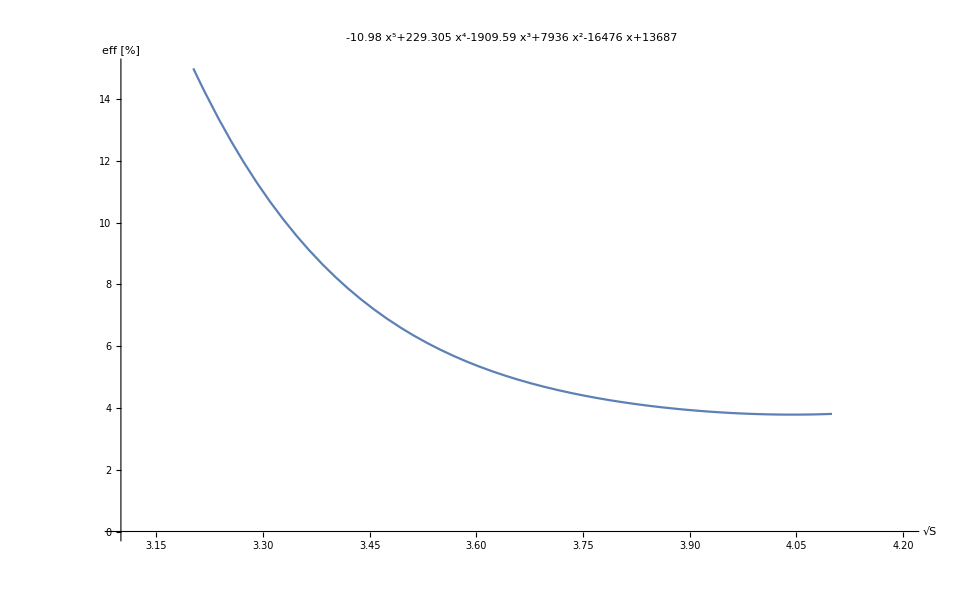

Xi_acc_plot.gif

```mathematica
xiAcc[x_]:=13687-16476*x+7936*x*x-1909.59*x*x*x+229.305*x*x*x*x-10.98*x*x*x*x*x;
xiaccPlot=Plot[xiAcc[x],{x,3.2,4.1},PlotRange->{{3.1,4.2},{0,15}},LabelStyle->Large,AxesLabel->{Sqrt[S],"eff [%]"},PlotLabel->Style[xiAcc[x],Large]]
Export["Xi_acc_plot.gif",xiaccPlot]
```

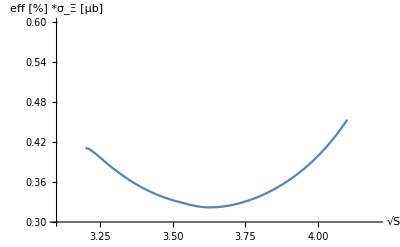

xi_eff_plot.gif

```mathematica
wydajnosc[s_]:=xiAcc[s]*ksiCS[s];
xiPlot=Plot[wydajnosc[x]/100,{x,3.2,4.1},PlotRange->{{3.1,4.2},{0.3,0.6}},AxesLabel->{Sqrt[S],"eff [%] *σ_Ξ [μb]"}]
Export["xi_eff_plot.gif",xiPlot]
```